## DNA (ψ̂)_00 Eigenvalue Analysis

/home/hemant/Desktop/workspace/Thesis/Results/DNA/Eigensystem/T00

0.25

10

*** Eigenvalues ***

*** Eigenvectors ***

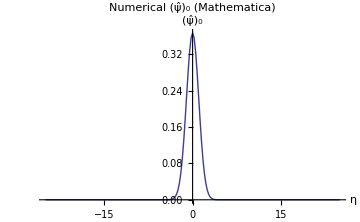
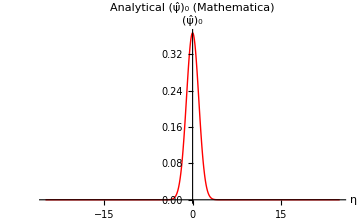

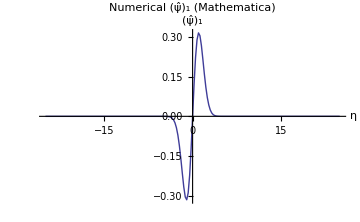
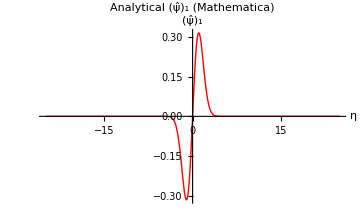

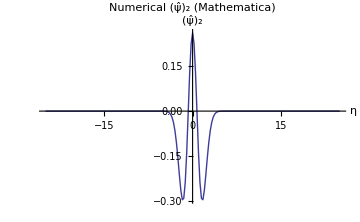
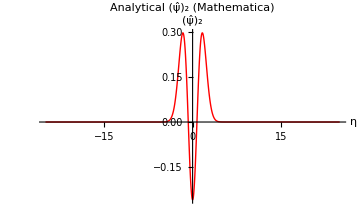

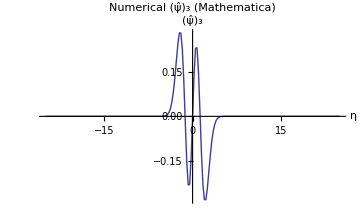
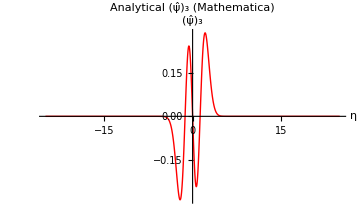

```mathematica
Needs["PlotLegends`"]
SetDirectory[FileNameJoin[{NotebookDirectory[]}]]

L=50;
m=100;
Δ=L/(2 m)//N
κ=10;
σ=1;

κσr=κ/σ

LastEval=10;

ηb=L/2;

max=2m+1;

(*Numerical*)
V[η_]:=If[Abs[η]≤ηb,(2 η^2)/κσr,(2 ηb^2)/κσr];

g0[η_]:=If[Abs[η]≤ηb,1,0];
g1[η_]:=If[Abs[η]≤ηb,0,1];

T̂[η1_,η2_] :=   g0[η1] *g0[ η2]*Exp[-(η1 - η2)^2]*Exp[-(V[η1] + V[η2])/2];
MT = Table[Δ T̂[ Δ R1, Δ R2],{R1, -m, m}, {R2, -m, m}] // N;
MatrixForm[MT];

Print["*** Eigenvalues ***"]
Subscript[Mλ, t] = Eigenvalues[MT];
Print["*** Eigenvectors ***"]
Subscript[Mψ, t] = Eigenvectors[MT];

Subscript[dataMψ, 0]=Table[{Δ j,Subscript[Mψ, t][[1,j+m+1]]},{j,-m,m}];
Subscript[dataMψ, 1]=Table[{Δ j,Subscript[Mψ, t][[2,j+m+1]]},{j,-m,m}];
Subscript[dataMψ, 2]=Table[{Δ j,Subscript[Mψ, t][[3,j+m+1]]},{j,-m,m}];
Subscript[dataMψ, 3]=Table[{Δ j,Subscript[Mψ, t][[4,j+m+1]]},{j,-m,m}];

(*Analytical*)

β=4;
μ=4/κσr//N;
c=((μ^2+2 β μ)^(1/2))/2//N;
Subscript[C, 0]=1/2 ((2 π)/((μ^2+2 β μ)^(1/2)))^(-1/4);
δ=2 c+μ+β;
b=1/2 ((δ^2-β^2)/δ)^(1/2)//N;
k=Log[δ/β]//N;
Subscript[e, 0]=((4 π)/δ)^(1/2)//N;
Subscript[MAψ, t][h_]:=Subscript[e, 0]*Exp[-k h];
nC[n_]:=(1/(2^n Factorial[n]))^(1/2);
ψ̂[n_,η_]:=2 Δ^(1/2)Subscript[C, 0] nC[n] HermiteH[n,b η] Exp[-(c η^2)/2];

(************************************************************)
Subscript[pdataMψ, 0]=ListLinePlot[-Subscript[dataMψ, 0],PlotStyle->{Thick},AxesLabel -> {η, Subscript[ψ̂, 0]},PlotLabel->"Numerical (ψ̂)_0 (Mathematica)",ImageSize->Medium,PlotRange->All];
Subscript[pMAψ, 0]=Plot[ψ̂[0,η],{η,-L/2,L/2},PlotStyle->{Thick,Red},AxesLabel -> {η, Subscript[ψ̂, 0]},PlotLabel->"Analytical (ψ̂)_0 (Mathematica)",ImageSize->Medium,PlotRange->All];
{Subscript[pdataMψ, 0],Subscript[pMAψ, 0]}
(************************************************************)
Subscript[pdataMψ, 1]=ListLinePlot[Subscript[dataMψ, 1],PlotStyle->{Thick},AxesLabel -> {η, Subscript[ψ̂, 1]},PlotLabel->"Numerical (ψ̂)_1 (Mathematica)",ImageSize->Medium,PlotRange->All];
Subscript[pMAψ, 1]=Plot[ψ̂[1,η],{η,-L/2,L/2},PlotStyle->{Thick,Red},AxesLabel -> {η, Subscript[ψ̂, 1]},PlotLabel->"Analytical (ψ̂)_1 (Mathematica)",ImageSize->Medium,PlotRange->All];
{Subscript[pdataMψ, 1],Subscript[pMAψ, 1]}
(************************************************************)
Subscript[pdataMψ, 2]=ListLinePlot[-Subscript[dataMψ, 2],PlotStyle->{Thick},AxesLabel -> {η, Subscript[ψ̂, 2]},PlotLabel->"Numerical (ψ̂)_2 (Mathematica)",ImageSize->Medium,PlotRange->All];
Subscript[pMAψ, 2]=Plot[ψ̂[2,η],{η,-L/2,L/2},PlotStyle->{Thick,Red},AxesLabel -> {η, Subscript[ψ̂, 2]},PlotLabel->"Analytical (ψ̂)_2 (Mathematica)",ImageSize->Medium,PlotRange->All];
{Subscript[pdataMψ, 2],Subscript[pMAψ, 2]}
(************************************************************)
Subscript[pdataMψ, 3]=ListLinePlot[Subscript[dataMψ, 3],PlotStyle->{Thick},AxesLabel -> {η, Subscript[ψ̂, 3]},PlotLabel->"Numerical (ψ̂)_3 (Mathematica)",ImageSize->Medium,PlotRange->All];
Subscript[pMAψ, 3]=Plot[ψ̂[3,η],{η,-L/2,L/2},PlotStyle->{Thick,Red},AxesLabel -> {η, Subscript[ψ̂, 3]},PlotLabel->"Analytical (ψ̂)_3 (Mathematica)",ImageSize->Medium,PlotRange->All];
{Subscript[pdataMψ, 3],Subscript[pMAψ, 3]}
(************************************************************)


fsTitle=24;
fsAxesLabel=24;
fs2=18;
```

Comparison of Eigenfunctions - Numerical and Analytical

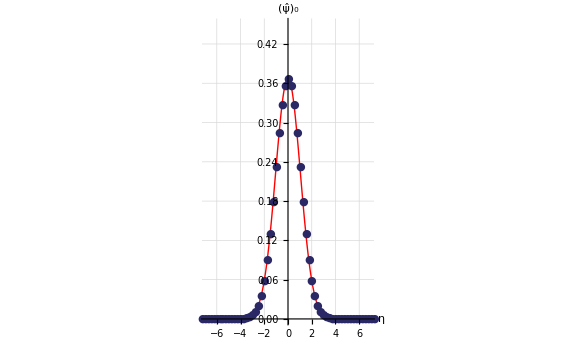

CreateDirectory::filex: "/home/hemant/Desktop/workspace/Thesis/Results/DNA/Eigensystem/T00/0.25/" already exists.

/home/hemant/Desktop/workspace/Thesis/Results/DNA/Eigensystem/T00/0.25

0.25/nVa_psi_t00_t0_L50_m100_k10_etab25.pdf

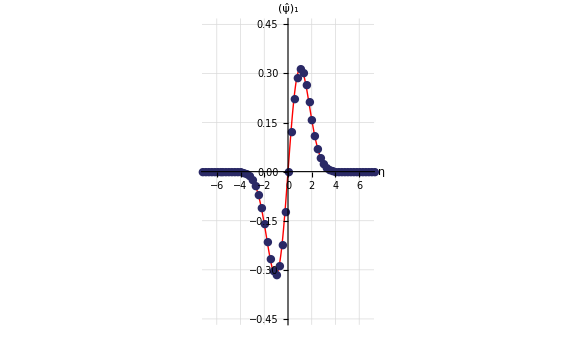

CreateDirectory::filex: "/home/hemant/Desktop/workspace/Thesis/Results/DNA/Eigensystem/T00/0.25/" already exists.

/home/hemant/Desktop/workspace/Thesis/Results/DNA/Eigensystem/T00/0.25

0.25/nVa_psi_t00_t1_L50_m100_k10_etab25.pdf

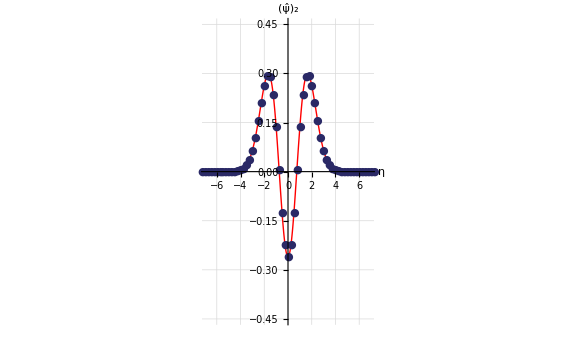

CreateDirectory::filex: "/home/hemant/Desktop/workspace/Thesis/Results/DNA/Eigensystem/T00/0.25/" already exists.

/home/hemant/Desktop/workspace/Thesis/Results/DNA/Eigensystem/T00/0.25

0.25/nVa_psi_t00_t2_L50_m100_k10_etab25.pdf

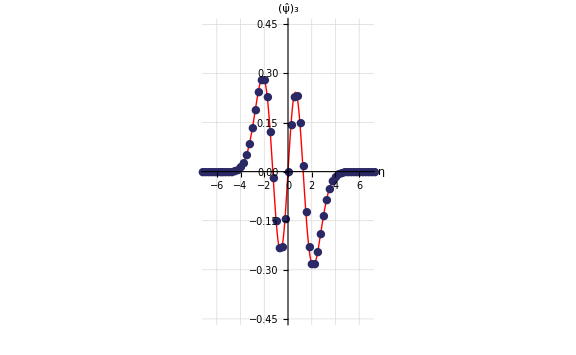

CreateDirectory::filex: "/home/hemant/Desktop/workspace/Thesis/Results/DNA/Eigensystem/T00/0.25/" already exists.

/home/hemant/Desktop/workspace/Thesis/Results/DNA/Eigensystem/T00/0.25

0.25/nVa_psi_t00_t3_L50_m100_k10_etab25.pdf

```mathematica
xRange=7;
yRange=0.45;

t=0;
p1=ListPlot[-Subscript[dataMψ, t],PlotStyle->{Thick,Dashed,Darker[ColorData[1,1]]},PlotMarkers->{"●"},PlotRange->All];
p2=Plot[ψ̂[t,η],{η,-L/2,L/2},PlotStyle->{Thick,Red},PlotRange->All];
{p1,p2};

legend={{Graphics[{Thick,Dashed,Darker[ColorData[1,1]],PointSize[Large],Point[{1,0}],Line[{{0,0},{2,0}}]}],Style["Numerical",FontSize->fs2]},{Graphics[{Thick,Red,Line[{{0,0},{2,0}}]}],Style["Analytical",FontSize->fs2]}};
EfunPlotψ=ShowLegend[Show[{p2,p1},PlotRange->{{-xRange,xRange},{0,yRange}},ImageSize->Large,(*PlotLabel->Style["Eigenfunction Plot (t="<>ToString[t]<>")",FontSize->fsTitle],*)GridLines->Automatic,GridLinesStyle->Directive[LightGray,Dashed],AxesLabel -> {Style["η",FontSize->fsAxesLabel],Style[Subscript["ψ̂",ToString[t]],FontSize->fsAxesLabel]},LabelStyle->{"Times",FontSize->fs2},ImageSize->Large],{legend,LegendShadow->None,LegendBorder->None,LegendBackground->Opacity[0],ShadowBackground->Opacity[0],LegendSize->0.5,LegendPosition->{0.3,0.2}}]

CreateDirectory[ToString[Δ]]
Export[ToString[Δ]<>"/nVa_psi_t00_t"<>ToString[t]<>"_L"<>ToString[L]<>"_m"<>ToString[m]<>"_k"<>ToString[κ]<>"_etab"<>ToString[ηb]<>".pdf",EfunPlotψ]

t=1;
p1=ListPlot[Subscript[dataMψ, t],PlotStyle->{Thick,Dashed,Darker[ColorData[1,1]]},PlotMarkers->{"●"},PlotRange->All];
p2=Plot[ψ̂[t,η],{η,-L/2,L/2},PlotStyle->{Thick,Red},PlotRange->All];
{p1,p2};

legend={{Graphics[{Thick,Dashed,Darker[ColorData[1,1]],PointSize[Large],Point[{1,0}],Line[{{0,0},{2,0}}]}],Style["Numerical",FontSize->fs2]},{Graphics[{Thick,Red,Line[{{0,0},{2,0}}]}],Style["Analytical",FontSize->fs2]}};
EfunPlotψ=ShowLegend[Show[{p2,p1},PlotRange->{{-xRange,xRange},{-yRange,yRange}},ImageSize->Large,(*PlotLabel->Style["Eigenfunction Plot (t="<>ToString[t]<>")",FontSize->fsTitle],*)GridLines->Automatic,GridLinesStyle->Directive[LightGray,Dashed],AxesLabel -> {Style["η",FontSize->fsAxesLabel],Style[Subscript["ψ̂",ToString[t]],FontSize->fsAxesLabel]},LabelStyle->{"Times",FontSize->fs2},ImageSize->Large],{legend,LegendShadow->None,LegendBorder->None,LegendBackground->Opacity[0],ShadowBackground->Opacity[0],LegendSize->0.5,LegendPosition->{0.3,0.2}}]

CreateDirectory[ToString[Δ]]
Export[ToString[Δ]<>"/nVa_psi_t00_t"<>ToString[t]<>"_L"<>ToString[L]<>"_m"<>ToString[m]<>"_k"<>ToString[κ]<>"_etab"<>ToString[ηb]<>".pdf",EfunPlotψ]

t=2;
p1=ListPlot[Subscript[dataMψ, t],PlotStyle->{Thick,Dashed,Darker[ColorData[1,1]]},PlotMarkers->{"●"},PlotRange->All];
p2=Plot[ψ̂[t,η],{η,-L/2,L/2},PlotStyle->{Thick,Red},PlotRange->All];
{p1,p2};

legend={{Graphics[{Thick,Dashed,Darker[ColorData[1,1]],PointSize[Large],Point[{1,0}],Line[{{0,0},{2,0}}]}],Style["Numerical",FontSize->fs2]},{Graphics[{Thick,Red,Line[{{0,0},{2,0}}]}],Style["Analytical",FontSize->fs2]}};
EfunPlotψ=ShowLegend[Show[{p2,p1},PlotRange->{{-xRange,xRange},{-yRange,yRange}},ImageSize->Large,(*PlotLabel->Style["Eigenfunction Plot (t="<>ToString[t]<>")",FontSize->fsTitle],*)GridLines->Automatic,GridLinesStyle->Directive[LightGray,Dashed],AxesLabel -> {Style["η",FontSize->fsAxesLabel],Style[Subscript["ψ̂",ToString[t]],FontSize->fsAxesLabel]},LabelStyle->{"Times",FontSize->fs2},ImageSize->Large],{legend,LegendShadow->None,LegendBorder->None,LegendBackground->Opacity[0],ShadowBackground->Opacity[0],LegendSize->0.5,LegendPosition->{0.3,-0.6}}]

CreateDirectory[ToString[Δ]]
Export[ToString[Δ]<>"/nVa_psi_t00_t"<>ToString[t]<>"_L"<>ToString[L]<>"_m"<>ToString[m]<>"_k"<>ToString[κ]<>"_etab"<>ToString[ηb]<>".pdf",EfunPlotψ]

t=3;
p1=ListPlot[Subscript[dataMψ, t],PlotStyle->{Thick,Dashed,Darker[ColorData[1,1]]},PlotMarkers->{"●"},PlotRange->All];
p2=Plot[-ψ̂[t,η],{η,-L/2,L/2},PlotStyle->{Thick,Red},PlotRange->All];
{p1,p2};

legend={{Graphics[{Thick,Dashed,Darker[ColorData[1,1]],PointSize[Large],Point[{1,0}],Line[{{0,0},{2,0}}]}],Style["Numerical",FontSize->fs2]},{Graphics[{Thick,Red,Line[{{0,0},{2,0}}]}],Style["Analytical",FontSize->fs2]}};
EfunPlotψ=ShowLegend[Show[{p2,p1},PlotRange->{{-xRange,xRange},{-yRange,yRange}},ImageSize->Large,(*PlotLabel->Style["Eigenfunction Plot (t="<>ToString[t]<>")",FontSize->fsTitle],*)GridLines->Automatic,GridLinesStyle->Directive[LightGray,Dashed],AxesLabel -> {Style["η",FontSize->fsAxesLabel],Style[Subscript["ψ̂",ToString[t]],FontSize->fsAxesLabel]},LabelStyle->{"Times",FontSize->fs2},ImageSize->Large],{legend,LegendShadow->None,LegendBorder->None,LegendBackground->Opacity[0],ShadowBackground->Opacity[0],LegendSize->0.5,LegendPosition->{0.3,0.2}}]

CreateDirectory[ToString[Δ]]
Export[ToString[Δ]<>"/nVa_psi_t00_t"<>ToString[t]<>"_L"<>ToString[L]<>"_m"<>ToString[m]<>"_k"<>ToString[κ]<>"_etab"<>ToString[ηb]<>".pdf",EfunPlotψ]
```